```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
```

# Fig 2

```mathematica
file=path<>"circles_data.hdf5";
data=Import[file, "Data"];
power = data["/power"];
freq = data["/freq"];
refl=data["/R_real"]+I data["/R_imag"];
```

```mathematica
powerRef=0;
npower=Length[power];
nfreq=Length[freq];
MinFreq=Min[freq];
MaxFreq=Max[freq];
MinPowerInd=2;
MaxPowerInd=npower-1;
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,MinPowerInd,MaxPowerInd},{l,0,1},{j,1,nfreq}];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{f0→6.54488,Γ→0.00180713,p→0.8099,α→6.76457×10^-7}

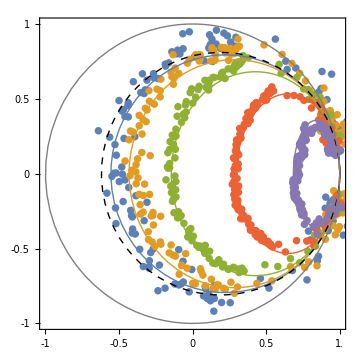

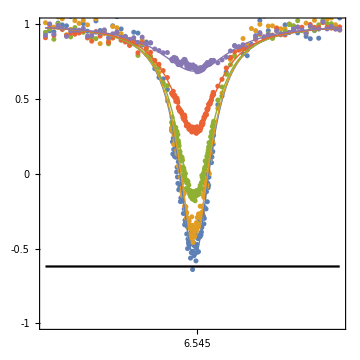

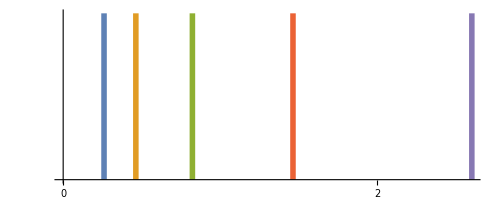

```mathematica
fit=FindFit[Flatten[tofit,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.00186},{p,0.793},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4,5};
ΩRabi =10^3 √(α 10^((power[[MinPowerInd;;MaxPowerInd]]-powerRef)/10))/.fit;

g1=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-1]],tofit[[i,2,;;,-1]]},{i,PlotIndices}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],
ParametricPlot[Evaluate@{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[Evaluate@{Re[1-(2 Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2  Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Gray,Thick]]
,Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

g2=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-4]],tofit[[i,1,;;,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{MinFreq,MaxFreq},{-1,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,MinFreq,MaxFreq},PlotRange->All,PlotStyle->Thick],
Plot[1-2p/.fit,{f,MinFreq,MaxFreq},PlotStyle->Black],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.53+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium]


g3=ParametricPlot[Evaluate[{#,x}&/@ΩRabi],{x,-0,0.5},PlotStyle->Thickness[0.01],Ticks->{Table[i,{i,0,10}],None},TicksStyle->Directive[Black,"Arial", 14]]
```

```mathematica
Export[path<>"circles.eps",g1]
Export[path<>"circles_real_part.eps",g2]
Export[path<>"Omega_rabi.eps",g3]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles_real_part.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\Omega_rabi.eps

# Fig 3

## Rabi

```mathematica
file=path<>"rabi_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
population = data["/y"];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{A→0.260845,B→0.498211,Ω→0.00598561,ϕo→-0.068079,TR→3.13178×10^15}

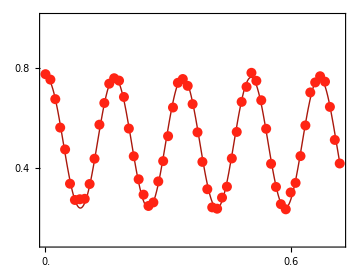

```mathematica
fit=FindFit[Transpose[{delays,population}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
Pratio01=(B2-A2)/(B2+A2);
P0ini=0.5;
r0=0.498;
g=Show[Plot[(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B)*(P0ini/r0)/.fit,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor["#FF2414"],Thick],PlotRange->{0.1,1}],ListPlot[Transpose@{delays/1000,population*(P0ini/r0)}, PlotStyle->{PointSize[0.02],RGBColor["#FF2414"]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"rabi.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\rabi.eps

## T1

```mathematica
file=path<>"t1_ramsey_echo_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
population = data["/y"];
T1Population=population[[1]];
T2Population=population[[3]];
```

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.487669 | 0.00806335 | {-0.504161,-0.471178}
B | 0.713394 | 0.00487792 | {0.703418,0.72337}
TR | 47634.9 | 1728.15 | {44100.5,51169.4}

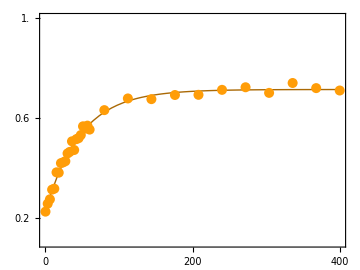

```mathematica
scale=0.5/0.498;
initguessS={{A,0.5},{B,0.8},{TR,50000}};
BoundS={1>A>-1,1>B>0,TR>0};
model=A*Exp[-t/TR]+B;
data=Transpose[{delays,T1Population*scale}];
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays/1000,T1Population*scale}];
g=Show[Plot[((nmf[t*1000]/.sparam)),{t,0,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#FF9D08"],Thick],PlotRange->{0.1,1}],ListPlot[dataS,PlotStyle->Directive[PointSize[0.02],RGBColor["#FF9D08"]]],FrameTicks->{{Table[0.2i,{i,-5,5}],None},{Table[100i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"t1.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\t1.eps

## T2

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | 0.275318 | 0.00825736 | {0.258429,0.292206}
B | 0.486677 | 0.0048306 | {0.476798,0.496557}
TR | 44380.6 | 2847.88 | {38556.1,50205.2}

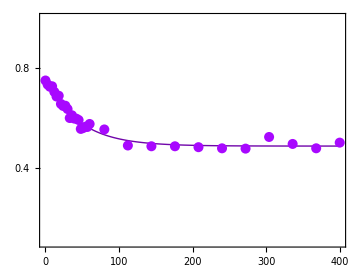

```mathematica
data=Transpose[{delays,T2Population*scale}];
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays/1000,T2Population*scale}];
g=Show[Plot[(nmf[t*1000]/.sparam),{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#A808FF"],Thick],PlotRange->{0.1,1}],ListPlot[dataS,PlotStyle->Directive[RGBColor["#A808FF"],PointSize[0.02]]], Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[100i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"t2.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\t2.eps

# Fig 4

```mathematica
file=path<>"transient_data.hdf5";
data=Import[file, "Data"];
delays = data["/time"];
power=data["/power"];
population= data["/y"];
```

```mathematica
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={1>A>-1,1>B>0,TR>0};
model=A*Exp[-t/TR]+B;
numberloop=Length[population];
fit=Table[NonlinearModelFit[Transpose[{delays[[loopi]],population[[loopi]]}],{model,BoundS},initguessS,t],{loopi,1,numberloop}];
Tpump=Table[TR/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
σTpump=Table[fit[[loopi]]["ParameterErrors"][[3]],{loopi,1,numberloop}]
Gpump=1/(2*Pi*Tpump);
Amp=Table[A/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
Bs=Table[B/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
```

{57159.9,12148.6,18720.6,25647.7,51172.1,8363.78,7097.11,8478.45}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{13028.6,658.391,1252.4,1535.37,8211.03,912.858,522.888,466.732}

{0.040253,0.505407,0.411227,0.30498,0.134526,0.477062,0.530892,0.535483}

{0.81169,0.253833,0.335571,0.472974,0.644572,0.227697,0.207353,0.208112}

{G10→2.68557×10^-6,G21→0.0000375212,a→0.000813222}

48.1628

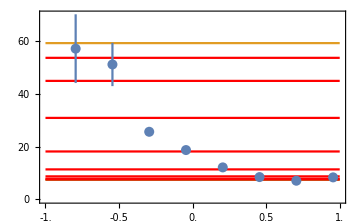

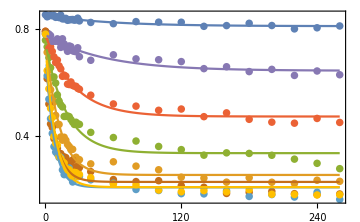

```mathematica
Needs["ErrorBarPlots`"]
T1guess=47634.93060222779;
G20=0.0018071254414408456;
G10guess=1/(2*Pi*T1fix);
Gfit2=FindFit[Transpose[{power,Gpump}],G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10)))),{{G10, G10guess},{G21,0.0005}, {a,6.764565019338307*^-7}},p]
G10fix=G10/.Gfit2;
T1fix=1/(2π G10fix);
G20/G21/.Gfit2
Omega=Sqrt[a*10^(power/10)]/.Gfit2;
toplotT=Table[{{Log10[10^3 Omega[[i]]],10^-3 Tpump[[i]]},ErrorBar[10^-3 σTpump[[i]]]},{i,1,Length@power}];
branching=Show[Plot[{10^-3 T1fix,10^-3 T1fix,10^-3/(π G21+2π G10fix)/.Gfit2},{x,-1,1}, PlotRange->All,PlotStyle->{None,Automatic,Automatic}],Plot[10^-3/(2*Pi*(G10+(G21*(a*10^(power/10))/((G20+G21)^2+2*(a*10^(power/10))))))/.Gfit2,{x,-1,1}, PlotRange->All,PlotStyle->Red],
ErrorListPlot[toplotT,PlotStyle->PointSize[0.02]],PlotRange->{0,70},Frame->True,FrameTicks->{{Table[0+20i,{i,0,4}],None},{Table[-1+0.5i,{i,0,4}],None}},ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]
Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{1,0},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,1,260},PlotRange->All],Frame->True,FrameTicks->{{Table[0.2i,{i,0,5}],None},{Table[40i,{i,0,10}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

```mathematica
FullSimplify[Solve[Log10[10^3 Sqrt[(a*10^(p/10))]]==x,p]]
```

{{p→(10 (x Log[100]-Log[1000000 a]))/Log[10]}}